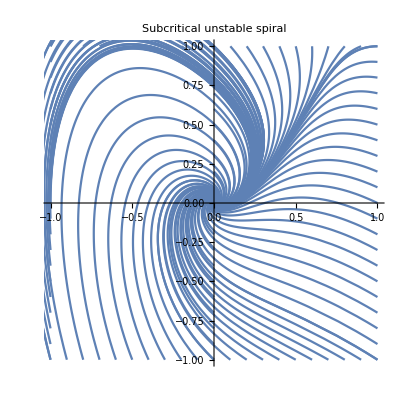

```mathematica
Clear["Global`*"]
minx=-1; maxx=1; miny=-1;  maxy=1; μ=-1;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10}, PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05,0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

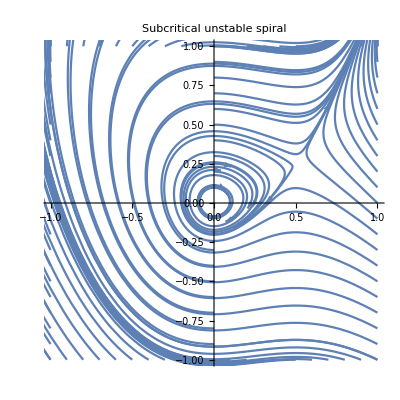

```mathematica
μ=0;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

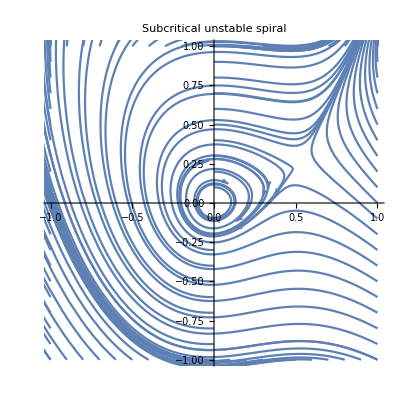

```mathematica
μ=0.03;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

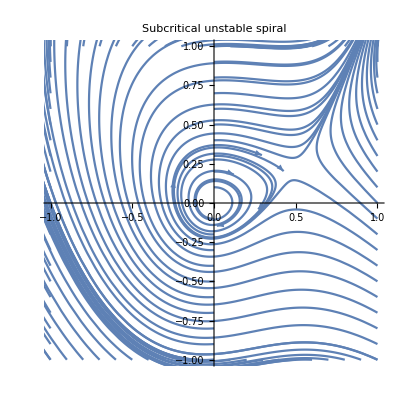

```mathematica
μ=0.066;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

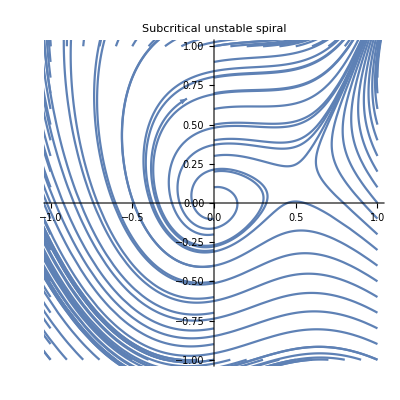

```mathematica
μ=0.2;
s[x0_,y0_]:=NDSolve[{x'[t]==μ*x[t]+y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0, y[0]==y0},{x,y},{t,0,10}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.05, 0.05, 0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

```mathematica
s=.
sol=DSolve[{x'[t]==u*x[t],x[0]==γ},x[t],t]//Flatten
```

{x[t]→ⅇ^(t u) γ}

```mathematica
Clear["Global`*"]
m = {{μ  - 2x,1}, {-1 + 2x, μ}};
V = Eigenvectors[m]
```

{{-(x+√(-1+2 x+x^2))/(-1+2 x),1},{-(x-√(-1+2 x+x^2))/(-1+2 x),1}}